All of the purple are comments from the instructor to student (read ME to YOU).  They should not appear in your lab writing.
v.25.22.23

# Exploring various walking styles

## How to walk like an Egyptian

Brian Geyer
Partner: Sparky Pomfret

Dates: 1/27/2009 to 1/30/2009, 2/2/2009^1

1: Note how consecutive dates are done.  Only the dates that data was collected in the lab should be listed.

Working in the gym we collected time and distance data that allowed us to compute our average speed for various walking styles.  My partner and I used a 30 meter (m)^2 tape and a stopwatch to collect our data.  We found that I was able to walk forward or backwards at roughly the same speed (2.19 meters/second (m/s) for forward and 2.15 m/s ^3 for backward) while I was much faster going forwards (5.91 m/s).  There is no standard value for how one walks but my results^4 (as you can see in the table later in the lab) compare favorably with others in the class.

2: The first time a unit is used it needs to be written out.
3. The next time only the abbreviation is needed
4: Even in a lab with no expected result I can make a claim about my data (here I state that I’m equally fast forward and backwards and much faster running).
NB: An abstract is no more than 4 sentences:
One sentence about what you did. 
One sentence about how you did it. (could be 2)
One sentence about what you got. Including numeric results and marks of quality if they exist.

## Table 1: times recorded at each interval BMG

Style of walking | four meters (s) | eight meters (s) | 12 meters (s) | 16 meters (s) | 20 meters (s)
walking | 3.72^1 | 5.12 | 6.66 | 8.93 | 10.87
running | 2.29 | 3.03 | 3.50 | 4.25 | 5.04
walk backwards | 5.00 | 6.82 | 8.76 | 10.87 | 12.22

1: These are times written down from the stopwatch, not measurements.  Therefore the terminal digit does not need to be 0, 1, 5, or 9.

```mathematica
walking={3.72,5.12,6.66,8.93,10.87};
running={2.29,3.03,3.5,4.25,5.04};
backwards={5,6.82,8.76,10.87,12.22};
```

```mathematica
modelwalk=LinearModelFit[walking,x,x];
modelrun=LinearModelFit[running,x,x];
modelback=LinearModelFit[backwards,x,x];
```

```mathematica
line=Plot[{modelwalk["BestFit"],modelrun["BestFit"],modelback["BestFit"]},{x,0,5.5},
Axes->None,
PlotStyle->{Orange,Pink,Purple},
PlotLegends->LineLegend[{Orange,Pink,Purple},{"Walking trendline", "Running trendline","Walking Backwards trendline"},LegendFunction->"Frame"],
ImageSize->Large];
```

```mathematica
points=ListPlot[{walking,running,backwards},
AxesLabel->{"t(s)","d(m)"},
PlotLabel->"Distnace vs. time of various walking styles BMG",
PlotStyle->{Orange,Pink,Purple},
PlotLegends->PointLegend[Automatic,{"Walking", "Running","Walking Backwards"},LegendFunction->"Frame"],
ImageSize->Large,
GridLines->Automatic];
```

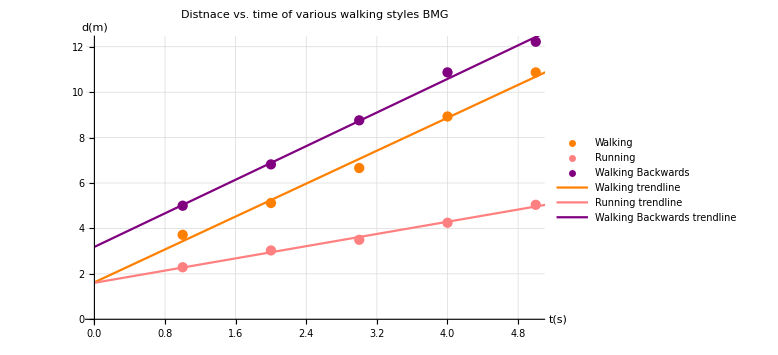

```mathematica
Show[points,line]
```

Comments on chart: 

• A legend is needed b/c there is more than one line plotted on the graph.  If you only have one set of points you should not have a legend.  Note the format of the title (x-variable vs. y-variable of verb noun, INITIALS of creator of graph)
• The axes labels use the correct abbreviation for the variable represented and the units in ( ).

## Table 2: times through the intervals BMG

```mathematica
{{style of walking, zero to four meters (s), four to eight meters (s), eight to 12 meters (s), 12 to 16 meters (s), 16 to 20 meters (s)}, {walking, 3.72, 1.4, 1.54, 2.27, 1.94}, {running, 2.29, 0.74, 0.47, 0.75, 0.79}, {walk backwards, 5.00, 1.82, 1.94, 2.11, 1.35}}
```

With the exception of the first interval (see below) here is how you would find the time that the runner is in each interval.  Each clock was started at the same time and as the runner reached the clock that clock was stopped.  So, the time in the 8m spot is the time that the runner was in both the zero to four zone and the four to eight zone.  I need to subtract the total time (0 to 8m) from the preceding section (0 to 4m) and I will have the time that the runner was in the second zone (4m to 8m).  The process is repeated for each subsequent interval.

```mathematica
time4to8m=time0to8m-time0to4m
```

in general this can be expanded in less specific notation

```mathematica
timeofinterval=totaltime-timeofpreceedingintervals
```

for walking we would have (taking the first row from Table 1):

```mathematica
time4to8m=5.12s-3.72s
```

1.4 s

```mathematica
time8to12m=6.66s-5.12s
```

1.54 s

```mathematica
time12to16m=8.93s-6.66s
```

2.27 s

```mathematica
time16to20m=10.87s-8.93s
```

1.94 s

you can see that these numbers form the first row of table 2.  the balance of table 2 is created in an identical manner

note that i do not need to show all the calculations, just a sample of each unique calculation.

## quality calculations

```mathematica
modelwalk["RSquared"]
modelrun["RSquared"]
modelback["RSquared"]
```

0.991086

0.993654

0.99611

My R^2 values are close to 1 and contain at least 2 nines. Reading from the rubric this makes my R^2 values “acceptable”.

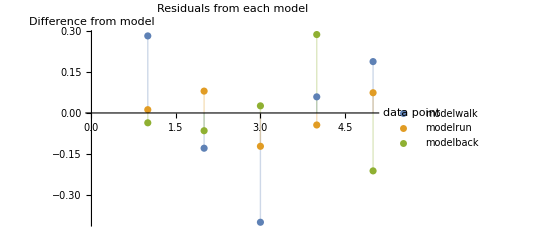

```mathematica
ListPlot[{modelwalk["FitResiduals"],
modelrun["FitResiduals"],
modelback["FitResiduals"]},
PlotLabel->"Residuals from each model",
AxesLabel->{"data point","Difference from model"},
Filling->Axis,
PlotLegends->PointLegend[Automatic,{"modelwalk", "modelrun","modelback"},LegendFunction->"Frame"]]
```

My residual graph shows no pattern and my values are all less that ±0.5.  These are both positive indicators.

Note that the residual graph does not have gridlines.
Also note that both marks of quality have a statement after them and there is a general summary in the conculsion.

## Peer data

In the gym we set up a track that was a straight line down the gym.  We set up timers (people with stopwatches) every 4.0 m creating a 20.0 m long track.  When the person started to move everyone started their watch and as the person passed a timer the timer stopped their watch. Each person went three times through the track moving a different way each time.
	The first problem we had was that each timer chose a different moment to stop his or her watch.  The third interval timer stopped when the first part of the mover got to them.  This created times that were smaller than the other intervals.  This shorter time created faster speeds for that interval. 
	The second problem was agreeing on when to start the watches.  The first time timer always started on the first movement, even if that movement was swinging arms or coiling to spring.  This timing method lead to longer times than for any other interval.  Once they started their time when the mover went to adjust their hair.  The longer times made for much smaller velocities.
	An error for this lab would be air resistance.  We all noticed that there was a breezing blowing on us when we were moving that we did not feel when standing still.  Air resistance is proportional to the speed of the mover.  The faster someone moves the more air resistance there was.  This made our shortest times longer than they otherwise would have been, which made our largest velocities smaller than they would have been.  
	Another error would have been that it takes time for the light to travel from the mover to the timer.  The mover will be going before the timer has started the watch.  This will lead to recording shorter times.  Having shorter times will mean that we have been find larger velocities^6.
	To record better data we could have used a photogate system similar to the ones used in professional sports.  When the runner begins to move forward they break a light beam that starts the timer.  As the pass through each interval they break a light beam, which stops the timer.  This would eliminate the timing problems and the timing error.  
	My walking forward and backward speeds are very similar.  By looking at the graph you can see that the trendlines of distance verses time have very similar slopes.  Knowing that the slope of the distance verses time graph is the velocity I can conclude that my two walking speeds are similar.  By looking at the R^2 numbers you can see that mine are very close to 1 (the closer R^2 is to 1 the higher the quality) this means that I was able to maintain a steady pace through the course.  You can see (by looking at the tables preceding this writing) that data from several other groups supports my result.  By looking at the residuals graph (below the calculations) you will see that there is no pattern and the numbers are fairly close to zero.  These are both indicators of quality results. The three people listed have similar interval times to mine so if we were to graph^7 them they would have similar results to mine^8. 
My walking speed (both forwards and backwards) are very similar and both are very different from my running speed.

6: We cannot remove the air from the room or change the fact that light moves at a finite speed so these are errors.  I do not expect you to be able to always properly connect the error to the appropriate shift but  I do think you can think out of the box and imagine some creative errors.

7:It would make a stronger argument to actually graph these, but that would be above and beyond the call of duty.

8:In the result section I talked about my results, how my results come logically from things learned in class, and how my results compare to others in the class.  If there were a way to computer % error I would mention how my results compared to what I should have gotten.  I also mention the quality of my graphs.

Note that all formatting rules were applied here.